```mathematica
DSolve[D[ph[t],{t,2}]+ph[t]==0,ph[t],t]
```

{{ph[t]→C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
Clear[t]
```

```mathematica
DSolve[D[ph[t],{t,2}]+Sin[ph[t]]==0,ph[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ph[t]→-2 JacobiAmplitude[1/2 √((2+C[1]) (t+C[2])^2),4/(2+C[1])]},{ph[t]→2 JacobiAmplitude[1/2 √((2+C[1]) (t+C[2])^2),4/(2+C[1])]}}

```mathematica
JacobiAmplitude[x+b,y+a]//FullSimplify
```

JacobiAmplitude[b+x,a+y]

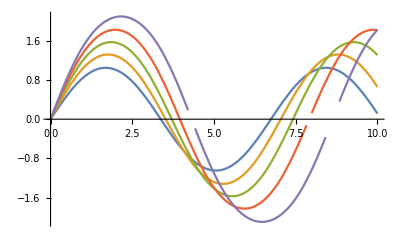

```mathematica
Plot[{2 JacobiAmplitude[0.5 √(t^2),4.],2 JacobiAmplitude[0.6123724356957945 √(t^2),2.6666666666666665],2 JacobiAmplitude[0.7071067811865476 √(t^2),2.],2 JacobiAmplitude[0.7905694150420949 √(t^2),1.6],2 JacobiAmplitude[0.8660254037844386 √(t^2),1.3333333333333333]},{t,0,10}]
```

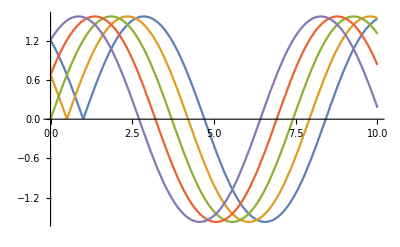

```mathematica
Plot[{2 JacobiAmplitude[(√((-1.+t)^2))/(√2),2],2 JacobiAmplitude[(√((-0.5+t)^2))/(√2),2],2 JacobiAmplitude[(√((0.+t)^2))/(√2),2],2 JacobiAmplitude[(√((0.5+t)^2))/(√2),2],2 JacobiAmplitude[(√((1.+t)^2))/(√2),2]},{t,0,10}]
```

```mathematica
Table[2 JacobiAmplitude[1/2 √((2+c1) (t+c2)^2),4/(2+c1)]/.c2->0,{c1,-1.9,2.,.5}]
```

{2 JacobiAmplitude[0.158114 √(t^2),40.],2 JacobiAmplitude[0.387298 √(t^2),6.66667],2 JacobiAmplitude[0.524404 √(t^2),3.63636],2 JacobiAmplitude[0.632456 √(t^2),2.5],2 JacobiAmplitude[0.724569 √(t^2),1.90476],2 JacobiAmplitude[0.806226 √(t^2),1.53846],2 JacobiAmplitude[0.880341 √(t^2),1.29032],2 JacobiAmplitude[0.948683 √(t^2),1.11111]}

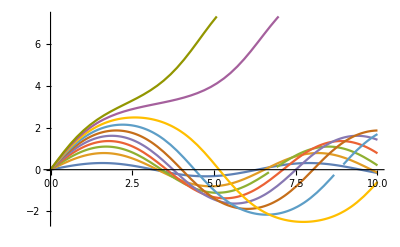

```mathematica
Plot[Evaluate@Table[2 JacobiAmplitude[1/2 √((2+c1) (t+c2)^2),4/(2+c1)]/.c2->0,{c1,-1.9,3.,.5}],{t,0,10}]
```

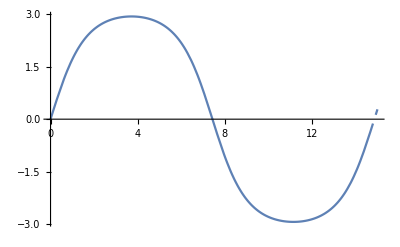

```mathematica
Plot[2 JacobiAmplitude[.99t,1/.99],{t,0,15}]
```

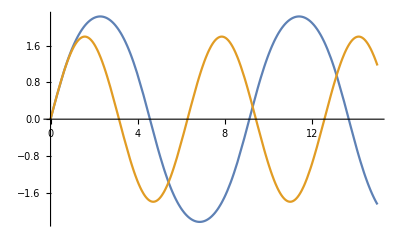

```mathematica
Plot[{2JacobiAmplitude[.9t,1/.9^2],1.8Sin[t]},{t,0,15}]
```

```mathematica
2.2/Pi
```

0.700282

```mathematica
Sqrt[.5/2]
```

0.5

```mathematica
Sqrt[.8/2]
```

0.632456

```mathematica
c JacobiDN[0,1/c]
```

c

```mathematica
D[JacobiAmplitude[c t,1/c^2],t]
```

c JacobiDN[c t,1/c^2]

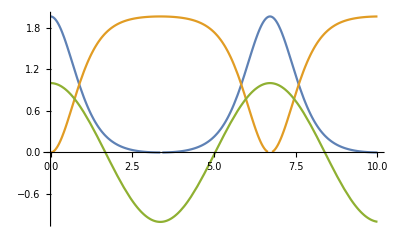

```mathematica
Plot[{1.9602 JacobiDN[0.99 t,1.0203040506070808]^2,1-Cos[2 JacobiAmplitude[0.99 t,1.0203040506070808]],Cos[Pi t/3.3566004720023486]},{t,0,10}]
```

```mathematica
Plot
```

```mathematica
{1/2(2c JacobiDN[c t,1/c^2])^2,1-Cos[2JacobiAmplitude[c t,1/c^2]]}/.c->1.2
```

{2.88 JacobiDN[1.2 t,0.694444]^2,1-Cos[2 JacobiAmplitude[1.2 t,0.694444]]}

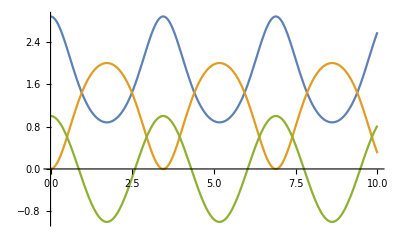

```mathematica
Plot[{2.88 JacobiDN[1.2 t,0.6944444444444444]^2,1-Cos[2 JacobiAmplitude[1.2 t,0.6944444444444444]],Cos[t Pi/halper[1.2]]},{t,0,10}]
```

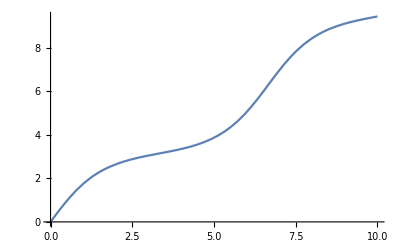

```mathematica
Plot[2JacobiAmplitude[c t,1/c^2]/.c->1.01,{t,0,10}]
```

```mathematica
Solve[(2c JacobiDN[c t,1/c^2])==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→InverseJacobiDN[0,1/c^2]/c}}

```mathematica
Re[InverseJacobiDN[10^-9,1/c^2]/c/.c->.99]
```

3.3566

Re[InverseJacobiDN[0.,1.5625]]

```mathematica
?Limit
```

```mathematica
Limit[InverseJacobiDN[x,1.5624999999999998],x->0]
```

InverseJacobiDN[0.,1.5625]

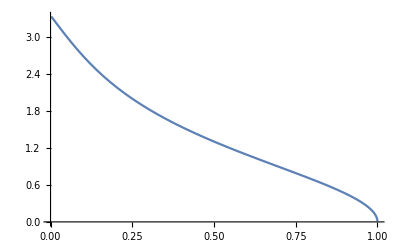

```mathematica
Plot[InverseJacobiDN[x,1/.99^2]/.99,{x,0,1}]
```

```mathematica
halper[c_]:=Re[InverseJacobiDN[10^-6,1/c^2]/c]
ke[c_]:=NIntegrate[1/2(2c JacobiDN[c t,1/c^2])^2,{t,0,halper[c]}]
pe[c_]:=NIntegrate[1-Cos[2JacobiAmplitude[c t,1/c^2]],{t,0,halper[c]}]
rho[c_]:=(ke[c]+pe[c])/halper[c]
drho[c_]:=(-6ke[c])/(ke[c]+pe[c])
```

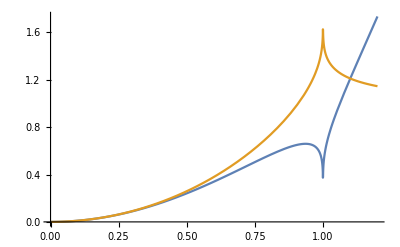

```mathematica
Plot[{ke[c]/halper[c],pe[c]/halper[c]},{c,0,1.2}]
```

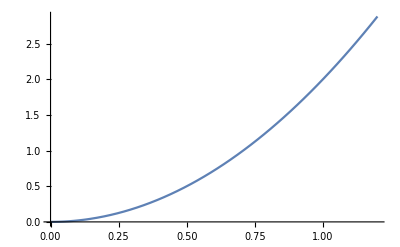

```mathematica
Plot[(ke[c]+pe[c])/halper[c],{c,0,1.2}]
```

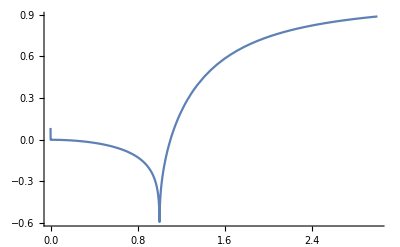

```mathematica
Plot[(ke[c]-pe[c])/(ke[c]+pe[c]),{c,0,3},PlotRange->All]
```

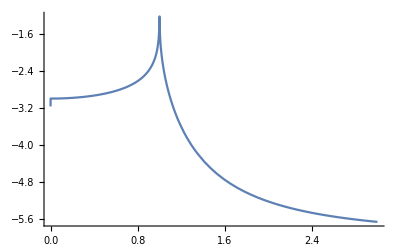

```mathematica
Plot[(-6ke[c])/(ke[c]+pe[c]),{c,0,3},PlotRange->All]
```

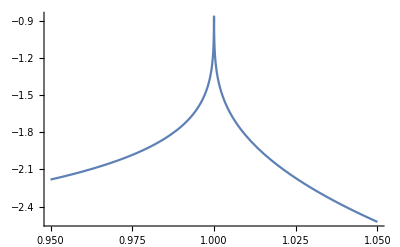

```mathematica
Plot[(-6ke[c])/(ke[c]+pe[c]),{c,.95,1.05},PlotRange->All]
```

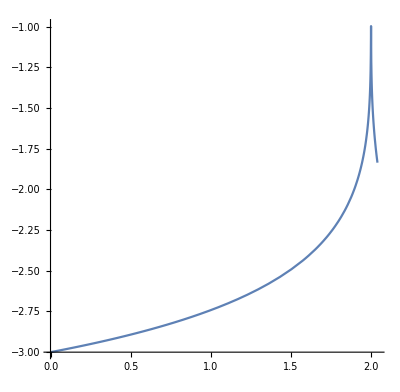

```mathematica
ParametricPlot[{(ke[c]+pe[c])/halper[c],(-6ke[c])/(ke[c]+pe[c])},{c,0.01,1.01},PlotRange->All]
```

```mathematica
rhotab=Table[{cc,rho[cc]},{cc,0,1,.001}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::nlim: t = Indeterminate is not a valid limit of integration.

```mathematica
rhotab2=Table[{10^lcc,rho[10^lcc]},{lcc,-2.1,0,.001}];
```

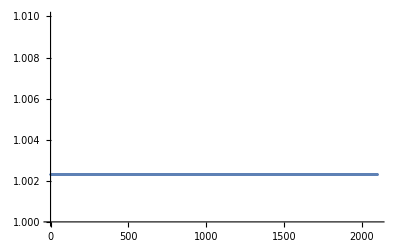

```mathematica
ListPlot[Table[rhotab2[[i,2]]*rhotab2[[i-1,1]]/(rhotab2[[i,1]]*rhotab2[[i-1,2]]),{i,2,Length[rhotab2]}],PlotRange->{1.,1.01}]
```

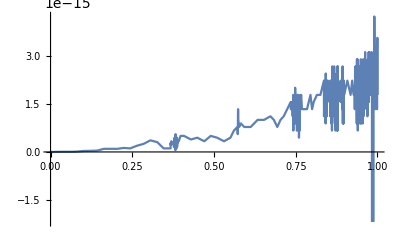

```mathematica
Plot[rho[c]-2c^2,{c,0,1}]
```

```mathematica
crho[rh_]:=Min[#[[1]]&/@Select[rhotab2,#[[2]]>rh&]]
```

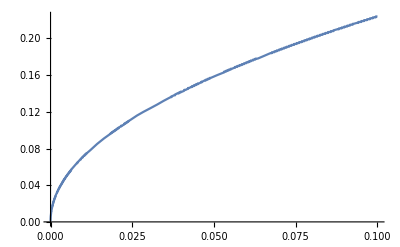

```mathematica
Plot[crho[rh],{rh,0,.1}]
```

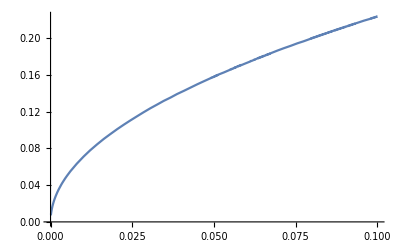

```mathematica
Plot[crho[rh],{rh,0,.1}]
```

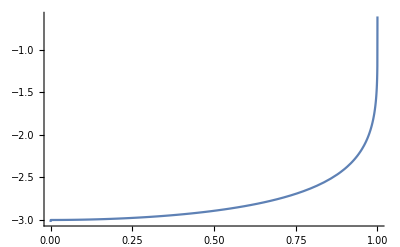

```mathematica
Plot[drho[c],{c,0,1},PlotRange->All]
```

```mathematica
2*.9^2
```

1.62

```mathematica
step=.0001
```

0.0001

```mathematica
rhs={};
For[cc=.9,
cc<1.05(*1.016*),
drh=drho[cc];
cc=cc(1-drh*.001/2);
rhs=rhs~Join~{2cc^2};
,
None;
]
```

```mathematica
rhs2={};
For[cc=.9,
cc<1.05,
drh=drho[cc];
cc=cc*Exp[-step*drh/2];
(*cc=cc(1-drh*.001/2);*)
rhs2=rhs2~Join~{2cc^2};
,
None;
]
```

```mathematica
ccs=Sqrt[#/2]&/@rhs;
```

```mathematica
drho[1.017]
```

-2.01468

```mathematica
Length[rhs]
```

120

```mathematica
drh
```

-1.97392

```mathematica
rhs[[-1]]/rhs[[-2]]
```

1.00197

```mathematica
scal=rhs2*Exp[2*las];
```

```mathematica
SortBy[Range[-50,-1],scal[[#]]&][[1]]
```

-29

```mathematica
scal[[-31;;-27]]
```

{2.18906,2.18901,2.189,2.18905,2.18914}

```mathematica
las[[-31;;-27]]
```

{0.03,0.029,0.028,0.027,0.026}

```mathematica
scal[[7;;10]]
```

{2.18833,2.18915,2.18996,2.19076}

```mathematica
las[[7;;10]]
```

{0.142,0.141,0.14,0.139}

```mathematica
.1415-.0285
Exp[%]
```

0.113

1.11963

```mathematica
Min[(rhs2*Exp[2*las])[[-50;;]]]
```

2.189

```mathematica
Select[Range[-100,1],(rhs2*Exp[2*las])[[#]]==%2088&]
```

{-29}

```mathematica
las[[-29]]//N
```

0.028

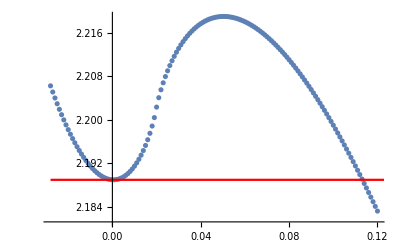

```mathematica
las=Range[step*(Length[rhs2]-1),0,-step];
Show[ListPlot[Transpose@{las-.028,rhs2*Exp[2*las]},PlotRange->All],
Plot[Min[(rhs2*Exp[2*las])[[-50;;]]],{la,0-.028,1-.028},PlotStyle->Red,PlotRange->All]
]
```

```mathematica
min=Min[(rhs2*Exp[2*las])[[-.05/step;;]]]
offset=las[[Select[Range[-.1/step,1],(rhs2*Exp[2*las])[[#]]==min&]]][[1]]
```

2.18797

0.0287

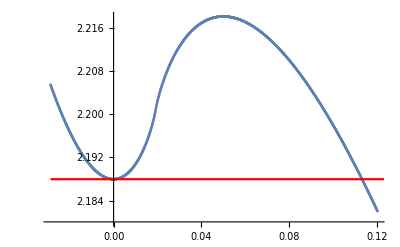

```mathematica
las=Range[step*(Length[rhs2]-1),0,-step];
Show[ListPlot[Transpose@{las-offset,rhs2*Exp[2*las]},PlotRange->All],
Plot[min,{la,0-offset,1-offset},PlotStyle->Red,PlotRange->All]
]
```

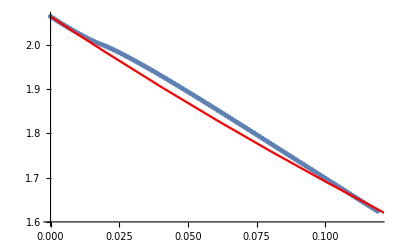

```mathematica
Show[ListPlot[Transpose@{Range[.001*(Length[rhs]-1),0,-.001],rhs},PlotRange->All],
Plot[rhs[[-1]]/Exp[2*la],{la,0,1},PlotStyle->Red,PlotRange->All]
]
```

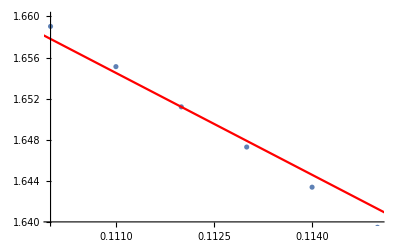

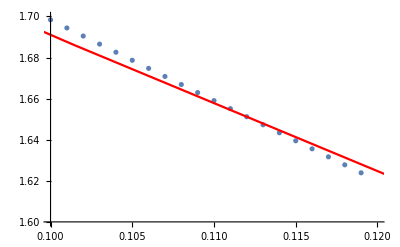

```mathematica
Show[ListPlot[Transpose@{Range[.001*(Length[rhs]-1),0,-.001],rhs},PlotRange->{{.11,.115},{1.64,1.66}}],
Plot[rhs[[-1]]/Exp[2*la],{la,0,1},PlotStyle->Red,PlotRange->All]
]
```

```mathematica
Exp[.112]
```

1.11851

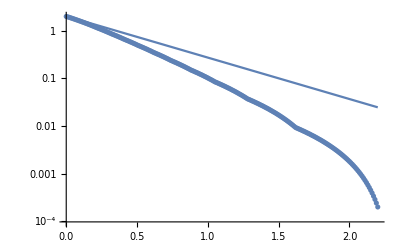

```mathematica
Show[ListLogPlot[Transpose@{Range[2.20,0,-.01],rhs[[;;221]]}],
LogPlot[2/Exp[2*la],{la,0,2.2}]
]
```

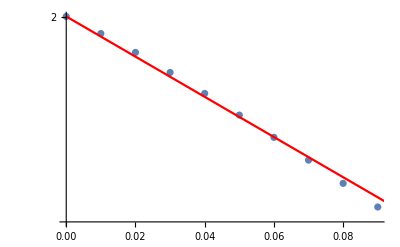

```mathematica
Show[ListLogPlot[Transpose@{Range[.09,0,-.01],rhs[[-10;;]]}],
LogPlot[rhs[[-1]]/Exp[2*la],{la,0,2.91},PlotStyle->Red]
]
```

```mathematica
ke[1]
```

2.

```mathematica
pe[1]
```

31.6225

```mathematica
halper[1]
```

ArcSech[1/10000000]

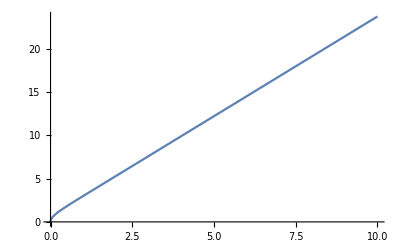

```mathematica
Plot[ArcSech[1/10^x],{x,0,10}]
```

```mathematica
halper[.99]
```

3.3566

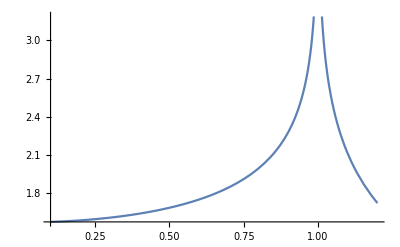

```mathematica
Plot[halper[c],{c,.1,1.2}]
```

```mathematica
halper[1.2]
```

1.72271

```mathematica
halper[.3]/2
```

1.60805

```mathematica
halper[.99]
```

3.3566

```mathematica
halper[.999]
```

4.49559